# 2 - Answers to challenges

## Using graphics primitives to annotate plots

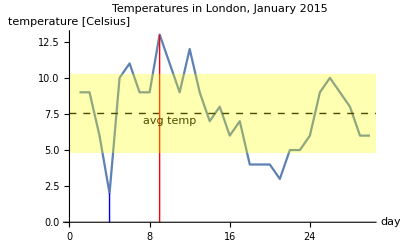

```mathematica
(* Challenge 1 *)

tempLondon = Table[{day, AirTemperatureData[Entity["City",{"London","GreaterLondon","UnitedKingdom"}], {2015,1,day, 13,0,0}, 
                                       UnitSystem->"Metric"]},
             {day, 1, 30}];
avgTemp = Mean[tempLondon]⟦2⟧ // QuantityMagnitude;
stdDevTemp = StandardDeviation[tempLondon]⟦2⟧ // QuantityMagnitude;
maxPt = First[MaximalBy[tempLondon, #⟦2⟧&] // QuantityMagnitude];
minPt = First[MinimalBy[tempLondon, #⟦2⟧&] // QuantityMagnitude];
ListLinePlot[tempLondon, 
	PlotLabel->"Temperatures in London, January 2015",
	AxesLabel->{"day", "temperature [Celsius]"},
	Epilog->{{Dashed, 
			Line[{{0,avgTemp}, {31,avgTemp}}]},
	        Text["avg temp", {10, avgTemp-0.5}],
	        
	        {Thin, Red,
	        Line[{maxPt, {maxPt⟦1⟧,0}}]},
	        {Thin, Blue,
	        Line[{minPt, {minPt⟦1⟧,0}}]},
	        
	        RGBColor[1,1,0,0.3],
	        Rectangle[{0,avgTemp-stdDevTemp}, {31,avgTemp+stdDevTemp}]}
]
```

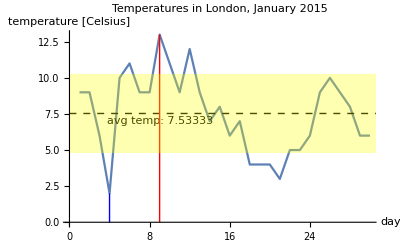

```mathematica
(* Challenge 2 *)

avgTemp = Mean[tempLondon]⟦2⟧ // QuantityMagnitude;
stdDevTemp = StandardDeviation[tempLondon]⟦2⟧ // QuantityMagnitude;
maxPt = First[MaximalBy[tempLondon, #⟦2⟧&] // QuantityMagnitude];
minPt = First[MinimalBy[tempLondon, #⟦2⟧&] // QuantityMagnitude];
ListLinePlot[tempLondon, 
	PlotLabel->"Temperatures in London, January 2015",
	AxesLabel->{"day", "temperature [Celsius]"},
	Epilog->{{Dashed, 
			Line[{{0,avgTemp}, {31,avgTemp}}]},
	        Text[Row[{"avg temp: ", N[avgTemp, 2]}], 
	             {9, avgTemp-0.5}],
	        
	        {Thin, Red,
	        Line[{maxPt, {maxPt⟦1⟧,0}}]},
	        {Thin, Blue,
	        Line[{minPt, {minPt⟦1⟧,0}}]},
	        
	        RGBColor[1,1,0,0.3],
	        Rectangle[{0,avgTemp-stdDevTemp}, {31,avgTemp+stdDevTemp}]}
]
```

```mathematica
Clear[tempLondon]
```

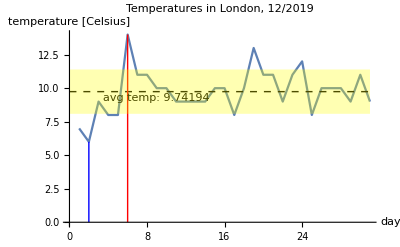

```mathematica
(* Challenge 3 *)

tempPlot[year_, month_] := Module[
	{tempLondon, avgTemp, stdDevTemp, maxPt, minPt},
	
	tempLondon = Table[{day, AirTemperatureData[Entity["City",{"London","GreaterLondon","UnitedKingdom"}], {year,month,day, 13,0,0}, 
                                       UnitSystem->"Metric"]},
             {day, 1, 31}]; (* // DeleteCases[#,{_,_Missing}]&; *)

	avgTemp = Mean[tempLondon]⟦2⟧ // QuantityMagnitude;
	stdDevTemp = StandardDeviation[tempLondon]⟦2⟧ // QuantityMagnitude;
	maxPt = First[MaximalBy[tempLondon, #⟦2⟧&] // QuantityMagnitude];
	minPt = First[MinimalBy[tempLondon, #⟦2⟧&] // QuantityMagnitude];

	ListLinePlot[tempLondon, 
		PlotLabel->Row[{"Temperatures in London, ", month, "/", year}],
		AxesLabel->{"day", "temperature [Celsius]"},
		Epilog->{{Dashed, 
			Line[{{0,avgTemp}, {31,avgTemp}}]},
	        Text[Row[{"avg temp: ", N[avgTemp, 2]}], 
	             {9, avgTemp-0.5}],
	        
	        {Thin, Red,
	        Line[{maxPt, {maxPt⟦1⟧,0}}]},
	        {Thin, Blue,
	        Line[{minPt, {minPt⟦1⟧,0}}]},
	        
	        RGBColor[1,1,0,0.3],
	        Rectangle[{0,avgTemp-stdDevTemp}, {31,avgTemp+stdDevTemp}]}]
]

tempPlot[2019,12]
```

```mathematica
maxPt = First@MaximalBy[tempLondon, #⟦2⟧&]
```

{9,13 °C}

## Creating custom plots

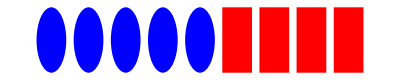

```mathematica
(* Challenge 1 *)

disks = Table[Disk[{x,0}, 0.4], {x, 1, 5}];
squares = Table[Rectangle[{x-0.4,-0.4}, {x+0.4,0.4}], {x, 6, 9}];
Graphics[Join[{Blue}, disks, {Red}, squares]]
```

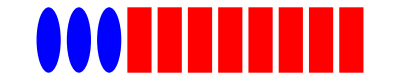

```mathematica
(* Challenge 2 *)

diskSquares[ndisks_, nsquares_] := Module[
	{disks, squares},

	disks = Table[Disk[{x,0}, 0.4], {x, 1, ndisks}];
	squares = Table[Rectangle[{x-0.4,-0.4}, {x+0.4,0.4}], 
	                {x, ndisks+1, ndisks+nsquares}];
	Join[{Blue}, disks, {Red}, squares]
]

Graphics[diskSquares[3, 8]]
```

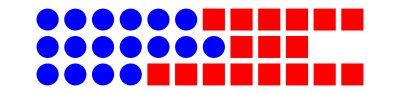

```mathematica
(* Challenge 3 *)

diskSquares[ndisks_, nsquares_, origin_] := Module[
	{disks, squares},

	disks = Table[Disk[{x,0}+origin, 0.4], {x, 1, ndisks}];
	squares = Table[Rectangle[{x-0.4,-0.4}+origin, {x+0.4,0.4}+origin], 
	                {x, ndisks+1, ndisks+nsquares}];
	Join[{Blue}, disks, {Red}, squares]
]

Graphics[{
	diskSquares[4, 8, {0,0}],
	diskSquares[7, 3, {0,1}],
	diskSquares[6, 6, {0,2}]}]
```

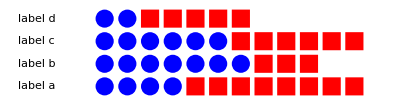

```mathematica
(* Challenge 4 *)

diskSquarePlot[data_, labels_] := Module[
	{shapes, placedLabels},

	shapes = Table[diskSquares[data⟦n,1⟧, data⟦n,2⟧, {2, n}],
	               {n, 1, Length[data]}];
	placedLabels = Table[Text[labels⟦n⟧, {0, n}], 
	                     {n, 1, Length[labels]}];

	Graphics[Join[shapes, placedLabels]]
]

diskSquarePlot[{{4, 8}, {7, 3}, {6, 6}, {2, 5}},
               {"label a", "label b","label c","label d"}]
```